### Code for mean-field solutions to “Dynamics of growth, death, and competition in sessile organisms” Author: Eddie Lee, edlee@santafe.edu

```mathematica
Clear["Global`*"]
```

## Independent compartment model

#### Discrete model at stationarity

```mathematica
r0=1;
dr=.5;  (*linear bin width*)
abar=60/5;  (*growth rate coefficient*)
cm=.1;
Abar=2/4 abar cm^(2/3); (*mortality rate constant*)
(*Abar=3/8 abar cm^(2/3)(α-1/3)*)
cdr=3/8 abar cm^(2/3);
imax=1000/dr;
α=1/3+Abar/cdr;
δ=.5;

g0=3;  (*number of new trees per unit time*)
rdot[r_]:=cdr r^(1/3)/dr;
μ[r_]:=Abar r^(-2/3);
α
```

1.66667

Calculate stationary distribution

```mathematica
nk={g0/(rdot[r0]+μ[r0])};
nk=Join[nk,Table[rdot[r0+dr(i-1)]/(rdot[r0+dr i]+μ[r0+dr i]),{i,2,imax}]];
For[i=2,i≤imax,i++,
nk[[i]]=nk[[i]]*nk[[i-1]]];
```

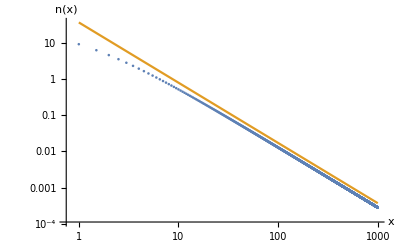

```mathematica
ListLogLogPlot[{Table[{(i-1) dr+r0,nk[[i]]},{i,1,imax}],{{r0,4nk[[1]]},{r0+imax dr,4(r0+imax dr)^-α nk[[1]]/r0^-α}}},Joined->{False,True},AxesLabel->{"x","n(x)"}]
```

#### Time evolution

```mathematica
tmax=60;
eqns=Join[{Subscript[n, 1]'[t]==g0-Subscript[n, 1][t](rdot[r0]+μ[r0])},Table[Subscript[n, i]'[t]==Subscript[n, i-1][t]rdot[r0+dr (i-2)]-Subscript[n, i][t](rdot[r0+dr (i-1)]+μ[r0+dr (i-1)]),{i,2,imax}]];
```

```mathematica
s=NDSolve[Join[eqns,Table[Subscript[n, i][0]==0,{i,1,imax}]],Table[Subscript[n, i],{i,1,imax}],{t,0,tmax},WorkingPrecision->45];
```

NDSolve::precw: The precision of the differential equation ({{TemporaryVariable$170199'[t]==3-3.23165 TemporaryVariable$170199[t],TemporaryVariable$170200'[t]==1.93899 TemporaryVariable$170199[t]-3.20608 TemporaryVariable$170200[t],«48»,«3950»},{},{},{},{}}) is less than WorkingPrecision (45.).

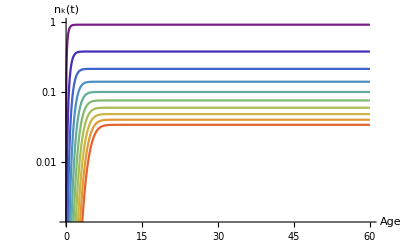

```mathematica
plot=LogPlot[Evaluate[Table[Subscript[n, i][t]/.s,{i,1,20,2}]],{t,0,tmax},PlotStyle->ColorData["Rainbow"]/@(Range[0,10]/10),AxesLabel->{"Age","n_k(t)"}]
```

General::munfl: -3.259293766843323×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.970728376889284×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.943418416740705×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

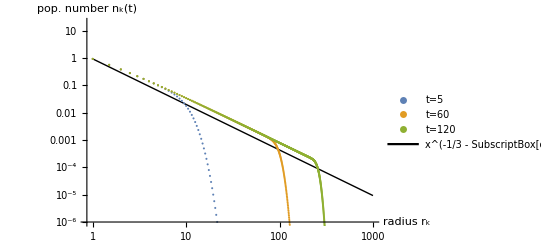

```mathematica
plot=ListPlot[{Legended[Table[{r0+(k-1) dr,Subscript[n, k][5]/.s//First},{k,1,imax}],"t=5"],
Legended[Table[{r0+(k-1)dr,Subscript[n, k][tmax/2]/.s//First},{k,1,imax}],"t=60"],
Legended[Table[{r0+(k-1) dr,Subscript[n, k][tmax]/.s//First},{k,1,imax}],"t=120"],
Style[Legended[{{r0,Subscript[n, 1][tmax]/.s//First},{r0+(imax-1) dr,(r0+(imax-1) dr)^-α/r0^-α(Subscript[n, 1][tmax]/.s//First)}},"x^(-1/3 - SubscriptBox[c, μ]/SubscriptBox[c, g])"],Black]},
PlotRange->{10^-6,20},AxesLabel->{"radius r_k","pop. number n_k(t)"},ScalingFunctions->{"Log","Log"},Joined->{False,False,False,True}]
(*Export[StringJoin[imgdr,"compet_nk_with_time.pdf"],plot]*)
```

## Discrete area and sunlight competition model

```mathematica
Clear["Global`*"]
```

#### Discrete model at stationarity

```mathematica
r0=1;
rmax=200;
dr=1;  (*linear bin width*)
cg=.3;  (*growth rate coefficient*)
cσ=.0;  (*area competition coeff*)
ca=.1;  (*root radius to area coef*)
cca=1;  (*radius to canopy area coef*)
ch=5;  (*radius to height coef*)
cλ=400/200^2;  (*sunlight competition coefficient*)
λ=.1;  (*light attenuation scale*)
cμ=.5; (*mortality rate constant*)
imax=rmax/dr;
tmax=400;
αr=2/3;
η1=1.8;
ν=2.1;  (*resource fluctuation exponent*)
A=rmax^(-(η1-2αr)(ν-1));
Δ=10;

g0=1000;  (*number of new trees per unit time*)
rdot[r_]:=cg r^(1/3)/dr;
μ[r_]:=cμ r^(-2/3);
a[r_]:=ca r^(4/3);  (*root area*)
ac[r_]:=cca r^2;  (*canopy area*)
h[r_]:=ch r^(2/3);
```

```mathematica
(*full pairwise equation*)
eqns={Subscript[n, 1]'[t]==g0-Subscript[n, 1][t](rdot[r0]+μ[r0]+cσ a[r0]Sum[Subscript[n, i][t]a[r0+(i-1) dr],{i,1,imax}]+cλ ac[r0]Sum[Subscript[n, i][t]ac[r0+(i-1)dr](1-Exp[-λ (h[r0+(i-1)dr]-h[r0])]),{i,2,imax}])};
eqns=Join[eqns,
Table[Subscript[n, i]'[t]==Subscript[n, i-1][t]rdot[r0+dr(i-2)]-Subscript[n, i][t](rdot[r0+dr (i-1)]+μ[r0+dr (i-1)]+cσ a[r0+(i-1)dr]Sum[Subscript[n, j][t]a[r0+(j-1) dr],{j,1,imax}]+cλ ac[r0+(i-1)dr]Sum[Subscript[n, j][t]ac[r0+(j-1)dr](1-Exp[-λ (h[r0+(j-1)dr]-h[r0+(i-1)dr])]),{j,i+1,imax}]),{i,2,imax}]
];
```

```mathematica
(*full pairwise equation with step function for light competition*)
eqns={Subscript[n, 1]'[t]==g0-Subscript[n, 1][t](rdot[r0]+μ[r0]+cσ a[r0]Sum[Subscript[n, i][t]a[r0+(i-1) dr],{i,1,imax}]+cλ ac[r0]Sum[Subscript[n, i][t]ac[r0+(i-1)dr]HeavisideTheta[h[r0+(i-1)dr]-h[r0]-Δ],{i,2,imax}])};
eqns=Join[eqns,
Table[Subscript[n, i]'[t]==Subscript[n, i-1][t]rdot[r0+dr(i-2)]-Subscript[n, i][t](rdot[r0+dr (i-1)]+μ[r0+dr (i-1)]+cσ a[r0+(i-1)dr]Sum[Subscript[n, j][t]a[r0+(j-1) dr],{j,1,imax}]+cλ ac[r0+(i-1)dr]Sum[Subscript[n, j][t]ac[r0+(j-1)dr]HeavisideTheta[h[r0+(j-1)dr]-h[r0+(i-1)dr]-Δ],{j,i+1,imax}]),{i,2,imax}]
];
```

```mathematica
(*MFT approximation for root area competition*)
eqns={Subscript[n, 1]'[t]==g0-Subscript[n, 1][t](rdot[r0]+μ[r0]+cσ A r0^((ν-1)(η1-2αr)))};
eqns=Join[eqns,
Table[Subscript[n, i]'[t]==Subscript[n, i-1][t]rdot[r0+dr(i-2)]-Subscript[n, i][t](rdot[r0+dr (i-1)]+μ[r0+dr (i-1)]+cσ A(r0+dr(i-2))^((ν-1)(η1-2αr))),{i,2,imax}]
];
```

```mathematica
(*Large equations require more time for resolving the derivatives.*)
SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->10.]
```

NDSolveOptions→{DefaultScanDiscontinuityTimeConstraint→1.,DefaultSolveTimeConstraint→10.}

```mathematica
initialConds=Table[Subscript[n, i][0]==0,{i,1,imax}];
s=NDSolve[Join[eqns,initialConds],Table[Subscript[n, i],{i,1,imax}],{t,0,tmax},WorkingPrecision->20];
```

NDSolve::precw: The precision of the differential equation ({{TemporaryVariable$98385'[t]==1000-TemporaryVariable$98385[t] (0.8+1/100 Plus[«195»]),TemporaryVariable$98386'[t]==0.3 TemporaryVariable$98385[t]-TemporaryVariable$98386[t] (0.692957+1/25 Plus[«194»]),TemporaryVariable$98387'[t]==0.377976 TemporaryVariable$98386[t]-TemporaryVariable$98387[t] (0.67305+9/100 Plus[«192»]),«46»,TemporaryVariable$98434'[t]==1.09779 TemporaryVariable$98433[t]-TemporaryVariable$98434[t] (1.14205+25 Plus[«139»]),«350»},{},{},{},{}}) is less than WorkingPrecision (20.).

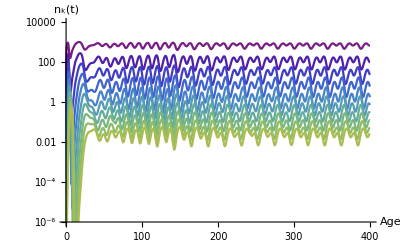

```mathematica
plot=LogPlot[Evaluate[Table[Subscript[n, i][t]/.s,{i,1,10,1}]],{t,0,tmax},PlotRange->{{0,tmax},{10^-6,10000}},PlotStyle->ColorData["Rainbow"]/@(Range[0,15]/15),AxesLabel->{"Age","n_k(t)"}]
```

Check log slope for convergence to equilibrium

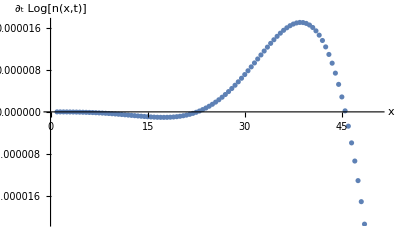

```mathematica
ListPlot[{Table[{(i-1) dx+x0,D[Log[Subscript[n, i][t]/.s],t]/.{t->tmax}//First},{i,1,imax}]},
Joined->{False,True},AxesLabel->{"x","∂_t Log[n(x,t)]"}]
```

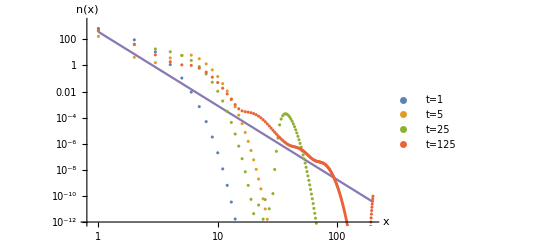

```mathematica
tlist={1,5,25,125};
ListLogLogPlot[Join[Table[Legended[Table[{(i-1) dr+r0,Subscript[n, i][t]/.s//First},{i,1,imax}],StringJoin["t=",ToString[t]]],{t,tlist}],
{Table[{(i-1) dr+r0,380((i-1) dr+r0)^(-6+1/3)},{i,1,imax}]}],
Joined->{False,False,False,False,True},AxesLabel->{"x","n(x)"},PlotRange->{10^-12,2000}]
```

```mathematica
(*Export to files*)
```

```mathematica
tlist={1,5,25,125};
fname="/Users/eddie/Dropbox/Research/forests/mathematica/nk_oscillations.csv";
Export[fname,Prepend[Table[Subscript[n, i][t]/.s//First,{t,tlist},{i,1,imax}],Table[r0+(i-1)dr,{i,1,imax}]]];
```

```mathematica
Export["/Users/eddie/Dropbox/Research/forests/mathematica/curves.csv",Prepend[Table[Subscript[n, i][t]/.
s//First,{i,1,10},{t,0,tmax,.1}],Table[t,{t,0,tmax,.1}]]];
```